## Companion code for the paper “Stars In Their Constellations: Great person or great team?” by Mindruta, Bercovitz, Mares, and Feldman. This notebook calculates the point estimates and 95% confidence intervals. Results are reported in Table 2a of the paper. init

```mathematica
SetDirectory[NotebookDirectory[]];
directory="https://raw.githubusercontent.com/MaximumScoreEstimator/MSE-Mathematica/master/";
Get[directory<>"mse.m"]
```

Loaded import.m

{noM,no,u,noAttr}=import[filename,"stream"] to load an upstream.

{noM,no,d,noAttr}=import[filename,"stream"] to load a downstream.

imports a file .xls or .xlsx or a tab delimited file .dat that includes data corresponding to an upstream (u) or downstream (d).

Datafiles consist of rows in the form {noM,no,attr1,attr2,...,attrn,noAttr}.

In the case of .xls or .xlsx files multiple sheets are joined - for example if each market resides in its own excel sheet.

__________________________________________________________________________________________________

{header,noM,noU,noD,noAttr,distanceMatrices,matchMatrix,mate}=import[filename_,"precomp",printflag_:False]

imports a file .xls or .xlsx or a tab delimited file .dat that includes precomputed matched data (distances between same attributes are already computed).

Datafiles consists of rows in the form {m,u,d,u1,d1,u2,d2,...,un,dn,matched (0 or 1)}.

In the case of .xls or .xlsx files multiple sheets are joined - for example if each market resides in its own excel sheet.

Loaded payoff.m

Cx[n] creates a list of n variables named x1,x2,...,xn.

payoff[m,i,j] returns the payoff of i-upstream and j-upstream in the m-market. 
It is used when the streams of u and d agents are imported separately (i.e. not in the precomputed format). It is assumed that u , d , and noAttr have been already assigned.

payoffDM[m,i,j] returns the payoff of i-upstream and j-upstream in the m-market.

It is used in the case of precomputed data. It is assumed that noAttr and distanceMatrices have been already assigned.

CpayoffMatrix[payoff(or payoffDM),noM_:noM,noU_:noU,noD_:noD,parallel_:False] calculates and assigns the payoffMatrix.
 
payoff is used when input data consist of separate u and d streams.

payoffDM is used for precomputed data.

CpayoffMatrix[solution_?VectorQ] substitutes the solution to all payoffMatrix's entries.

payoffMatrix2Positive[offset,payoffMatrix,epsilon_:0,sameoffset_:False] translates the payoffMatrix subtracting an offset and adding an epsilon. This function's main purpose is to make all elements positive.
epsilon is the minimum element per market. It's default value is 0.
If the sameoffset flag is set to False (which is the default value) then each market will be handled separately related to its minimum.
If the sameoffset flag is set to True then the offset equals the minimum element in the entire payoffMatrix.

Ctotalpayoff[payoffobject,mates] calculates the total payoff (i.e. the sum of payoffs) across all markets for the specific mates arrangement. This function accepts as a first argument the “payffobject”, which can either be the name of the payoff function or the payoffMatrix (in case we have already calculated all pair payoffs).

Loaded matching.m

generateAssignmentMatrix[payoffs,quotaU,quotaD], generates the optimal assignment of matches from the given matrix of payoffs for each match. The optimal assignment is the one that maximizes the total payoff (i.e. the sum of all payoffs) in a market. In an assignment matrix, each entry (i,j) is 1 if i and j are matched and 0 otherwise. The quota can be a number (the same for all streams) or a list that sets a specific quota per agent.
Notice that the quota is max number of matches per agent ( so in the data the real number of matches could be lower than the max).

CmatchMatrix[payoffMatrix_,quotaU_:1,quotaD_:1,p_:0]  
Calculates and creates/updates the global variable 'matchMatrix'.
If p is set to 0, it creates the matchMatrix by running the generateAssignmentMatrix routine for all markets.
If p is set to an integer from 1 to the 'number of Markets' then the p'th element of the matchMatrix is calculated.

Cquota[matchMatrix,function_:<|"upstream"→True,"downstream"→True|>] Calculates and creates/updates the global variable 'quota'.By default it calculates both streams quotas. It returns the association list quota = <|"upstream"->quotaU,"downstream"->quotaD|>. Quota is defined for each stream u and d.

Cmates[matchMatrix] simplifies the matchMatrix to a list of triples that define matches across all markets. It provides another way to express all the matching information that is, which upstream is matched with which downstream and in which market. The output consists of a list of lists of triples each of which has the following structure: {market_index,upstream_index,downstream_index}.
Output example:{{{1,1,3},{1,3,1},{1,3,2}},{{2,1,1},{2,2,1},{2,2,3},{2,3,2}}}. In this example we have 2 lists, one per market and each inner list contains the triples. Note that in market 1, upstream agent 2 is not contributing which is fine. 
This function is mainly used for the calculation of the total payoff - see Ctotalpayoff routine.

Cmate[matchMatrix] simplifies the matchMatrix from the original code by Santiago & Fox, to a matrix format which consists of lists of pairs, one pair per market. Here, each pair has the following structure: {{{1},{2},...,{noU within this market}},{{downstreams that are matched with upstream1},{downstreams that are matched with upstream2},...,{downstreams that are matched with upstream noU}}.
Example : {{{{1},{2},{3}},{{3},{},{1,2}}},{{{1},{2},{3}},{{1},{1,3},{2}}}}.  In this example, there are three upstream and three downstream agents in each market, indexed 1, 2, 3. In the first market, upstream 1 is matched with downstream 3, upstream 2 is not matched, and upstream 3 is matched with downstream 1 and  2. In the second market, upstream 1 is matched with downstream 1, upstream 2 with downstream 1 and 3, and upstream 3 with downstream 2.  
The mate=Cmate[matchMatrix] is later fed into the Cineqmembers routine.

Loaded inequalities.m

Cineqmembers[mate] generates all the members required to form the inequalities for many to many relationships defined by the mate. The produced list of lists of triples defines also the way inequalities are formed. At this time, inequalities are created to follow the theoretical proofs done by J Fox. CAUTION: ineqmembers is the largest object so it consumes a lot of memory. This is why we use MSEresources="Memory" when it is needed. Be careful because in the “Memory model”, ineqmembers are erased after being used for the dataArray calculation, in order to speed up the calculations.

Cinequalities[f,ineqmembers] apply properly the f function to ineqmembers to create inequalities. This routine is called by CdataArray internally where as a function it uses payoffMatrix[[##]]&.

Loaded dataArray.m

CdataArray[payoffMatrix,xlist,printflag] creates the dataArray. It works either using the "Speed" model or the "Memory" model. It uses ineqmembers and Cinequalities internally and for the memory model it erases ineqmembers after use.

Loaded objective.m

objective[dataArray,x1,x2,...,xn] defines the objective function to maximize the number of satisfied inequalities. An inequality is satisfied when the left side is weakly greater than the right side (>=).

objectiveV[dataArray,x1,x2,...,xn] is the verbose version of objective routine. It also uses groupIDs produced by CdataArray routine. It returns more information about how many inequalities are satisfied for each market. It is obviously slower than the plain objective and it is used as the final step after the maximization process.

Loaded maximize.m

maximize[dataArray_,noAttr_,method_:"DifferentialEvolution", permuteinvariant_:True, printflag_:True] is MSE specific and uses the optimize function. It uses the objective function (that counts the number of satisfied inequalities). It returns a list {max,{x1->value1, x2->value2, ...}, number of inequalities} where max is the maximum number of satisfied inequalities found and the solution of the maximization method {value1,value2,...}

Loaded confidence.m

pointIdentifiedCR[ssSize,numSubsamples,pointEstimate,args,groupIDs,dataArray,method,permuteinvariant,options] generates a confidence region estimate using subsampling.\r
Parameters:
ssSize - The size of each subsample to be estimated.
numSubsamples -The number of subsamples to use in estimating the confidence region.
pointEstimate - The point estimate to build the confidence region around (typically the output of pairwiseMSE).
objFunc - The objective function used in pairwiseMSE.
args - A list of unique symbols used in pairwiseMSE.
groupIDs - A data map used to generate the subsamples.
dataArray - The dataArray parameter used in pairwiseMSE.
options - An optional parameter specifying options. Available options are:
	progressUpdate - How often to print progress (0 to disable).Default=0. 
	confidenceLevel - The confidence level of the region.Default=.95.
	asymptotics - Type of asymptotics to use (nests or coalitions).Default=nests.
	subsampleMonitor - An expression to evaluate for each subsample.Default=Null.
	symmetric - True or False.If True,the confidence region will be symmetric.Default=False.

Loaded modifydata.m

store[var,printflag] is used for storing all global variables to "var" global variable before they are modified.  In that case they can restored later (with the restore[var] command).
Variables: {"header","noM","noU","noD","noAttr","distanceMatrices","matchMatrix","mate","quota","payoffMatrix","totalpayoff","dataArray"}}

restore[var,printflag] is used to restore all global variables from "var" global variable (when the last store[] command was used).
Variables: {"header","noM","noU","noD","noAttr","distanceMatrices","matchMatrix","mate","quota","payoffMatrix","totalpayoff","dataArray"}}

modify[m_,u_List,d_List,function_?AssociationQ:<|"unmatch"→False,"remove"→True,"quota_reset"→False,"quota_update"→False,"quota_update_upstream"->False,"quota_downstream_upstream"->False,"rematch"→False|>] 
modifies m's market upstream and/or downstream members. As a consequence payoffMatrix, matchMatrix, quota are modified.
If "unmatch"→True then it is supposed that the Transpose[u,d] are the matches we need to unmatch.
If "unmatch"→True and "quota_update_upstream"→True then the quota of the unmatched upstreams are reduced by one.
If "unmatch"→True and "quota_update_download"→True then the quota of the unmatched downstreams are reduced by one.
If "remove"→True and "quota_reset"→True then the quota of the selected for remove streams becomes equal to 0.
If "remove"→True and "quota_update"→True then the quota of the matched opposite stream are reduced because of the stream removal.
If "rematch"→True then the matchMatrix of the m'th market is re-calculated using the set quota.

{74266280,58993160,1}

## Import precomputed data

Load the data

```mathematica
filename="../data/stars_replication_input.dat";
```

```mathematica
import[filename,"precomp"];
{header,noM,noU,noD,noAttr,distanceMatrices,matchMatrix,mate}
```

{{market,upstreamid,downstreamid,cites_cites,kn_similarity,_sq (kn_similarity),cites_size,cites_experience,cites_rankcmd,domain_similarity,match},6,{1}}
 |  |  |  |

## Routines (calculate payoff matrix, inequalities members, dataArray)

```mathematica
CpayoffMatrix[payoffDM,noM,noU,noD];
```

```mathematica
Cineqmembers[mate];
```

```mathematica
CdataArray[payoffMatrix,Cx[noAttr-1]];
```

## Maximization

### Differential Evolution Method

The default DifferentialEvolution parameters:

option name | default value |  
"CrossProbability" | 0.5 | probability that a gene is taken from x_i
"InitialPoints" | Automatic | set of initial points 
"PenaltyFunction" | Automatic | function applied to constraints to penalize invalid points
"PostProcess" | Automatic | whether to post-process using local search methods 
"RandomSeed" | 0 | starting value for the random number generator
"ScalingFactor" | 0.6 | scale applied to the difference vector in creating a mate 
"SearchPoints" | Automatic | size of the population used for evolution 
"Tolerance" | 0.001 | tolerance for accepting constraint violations

```mathematica
?maximize
```

maximize[dataArray_,noAttr_,method_:"DifferentialEvolution", permuteinvariant_:True, printflag_:True] is MSE specific and uses the optimize function. It uses the objective function (that counts the number of satisfied inequalities). It returns a list {max,{x1->value1, x2->value2, ...}, number of inequalities} where max is the maximum number of satisfied inequalities found and the solution of the maximization method {value1,value2,...}

```mathematica
method={"DifferentialEvolution","CrossProbability"->0.5,"InitialPoints"->Automatic,"PenaltyFunction"->Automatic,"PostProcess"->Automatic,"RandomSeed"->12,"ScalingFactor"->0.6,"SearchPoints"->300,"Tolerance"->0.001};
sol=maximize[dataArray,noAttr,method];
```

The new ordering of attributes used for calculating the solutio order={5,4,3,2,1,6}

Method {DifferentialEvolution, CrossProbability -> 0.5, InitialPoints -> Automatic, PenaltyFunction -> Automatic, PostProcess -> Automatic, RandomSeed -> 12, ScalingFactor -> 0.6, SearchPoints -> 300, Tolerance -> 0.001}

Completed : {Number of satisfied inequalities→3731.,{kn_similarity→4.98191,_sq (kn_similarity)→-2.40165,cites_size→0.0664202,cites_experience→1.28895,cites_rankcmd→1.39831,domain_similarity→2.76088},Number of inequalities→3745}
Satisfied Ineqs Analysis:
 Market no | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33
Satisfied | 36 | 66 | 20 | 36 | 28 | 21 | 21 | 55 | 15 | 66 | 208 | 28 | 90 | 209 | 21 | 55 | 209 | 104 | 91 | 276 | 44 | 149 | 170 | 66 | 153 | 435 | 28 | 153 | 231 | 105 | 120 | 377 | 45
Total | 36 | 66 | 21 | 36 | 28 | 21 | 21 | 55 | 15 | 66 | 210 | 28 | 91 | 210 | 21 | 55 | 210 | 105 | 91 | 276 | 45 | 153 | 171 | 66 | 153 | 435 | 28 | 153 | 231 | 105 | 120 | 378 | 45
Percentage % | 100 | 100 | 95 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 99 | 100 | 99 | 100 | 100 | 100 | 100 | 99 | 100 | 100 | 98 | 97 | 99 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100

## Confidence Intervals

### execution

```mathematica
ssSize=28;numSubsamples=2500;alpha=0.05;
```

```mathematica
(*If you want to calculate confidence intervals with other subSamples please uncomment the code below*)
(*
(Print["Starting pointIdentified process where alpha = ",alpha];
pointIdentified=pointIdentifiedCR[ssSize,numSubsamples,sol[[2]], Cx[noAttr-1], groupIDs, dataArray,method,True,confidenceLevel->(1-alpha),asymptotics->nests, progressUpdate->10];
{pointIdentified,
ListPlot@Flatten[Map[
MapIndexed[Flatten@{#2,#1}&,#]&,
pointIdentified[[-1]]
],1]
})//AbsoluteTiming
*)
```

```mathematica
(*If you need to save the calculated list of subSamples please uncomment the code below*)
(*
savedGroups=randomGroups;
savedGroups>>"savedGroups.m";
savedGroups
savedGroups=.; (*clears the variable*)
*)
```

#### Run with saved subSamples (Random Groups)

```mathematica
savedGroups=<<"../data/savedGroupsReplication.m";
numSubsamples=Length[savedGroups]
```

2500

Starting pointIdentified process where alpha = 0.05

Iterations completed:10

Iterations completed:20

Iterations completed:30

Iterations completed:40

Iterations completed:50

Iterations completed:60

Iterations completed:70

Iterations completed:80

Iterations completed:90

Iterations completed:100

Iterations completed:110

Iterations completed:120

Iterations completed:130

Iterations completed:140

Iterations completed:150

Iterations completed:160

Iterations completed:170

Iterations completed:180

Iterations completed:190

Iterations completed:200

Iterations completed:210

Iterations completed:220

Iterations completed:230

Iterations completed:240

Iterations completed:250

Iterations completed:260

Iterations completed:270

Iterations completed:280

Iterations completed:290

Iterations completed:300

Iterations completed:310

Iterations completed:320

Iterations completed:330

Iterations completed:340

Iterations completed:350

Iterations completed:360

Iterations completed:370

Iterations completed:380

Iterations completed:390

Iterations completed:400

Iterations completed:410

Iterations completed:420

Iterations completed:430

Iterations completed:440

Iterations completed:450

Iterations completed:460

Iterations completed:470

Iterations completed:480

Iterations completed:490

Iterations completed:500

Iterations completed:510

Iterations completed:520

Iterations completed:530

Iterations completed:540

Iterations completed:550

Iterations completed:560

Iterations completed:570

Iterations completed:580

Iterations completed:590

Iterations completed:600

Iterations completed:610

Iterations completed:620

Iterations completed:630

Iterations completed:640

Iterations completed:650

Iterations completed:660

Iterations completed:670

Iterations completed:680

Iterations completed:690

Iterations completed:700

Iterations completed:710

Iterations completed:720

Iterations completed:730

Iterations completed:740

Iterations completed:750

Iterations completed:760

Iterations completed:770

Iterations completed:780

Iterations completed:790

Iterations completed:800

Iterations completed:810

Iterations completed:820

Iterations completed:830

Iterations completed:840

Iterations completed:850

Iterations completed:860

Iterations completed:870

Iterations completed:880

Iterations completed:890

Iterations completed:900

Iterations completed:910

Iterations completed:920

Iterations completed:930

Iterations completed:940

Iterations completed:950

Iterations completed:960

Iterations completed:970

Iterations completed:980
Iterations completed:990

Iterations completed:1000

Iterations completed:1010

Iterations completed:1020

Iterations completed:1030

Iterations completed:1040

Iterations completed:1050

Iterations completed:1060

Iterations completed:1070

Iterations completed:1080

Iterations completed:1090

Iterations completed:1100

Iterations completed:1110

Iterations completed:1120

Iterations completed:1130

Iterations completed:1140

Iterations completed:1150

Iterations completed:1160

Iterations completed:1170

Iterations completed:1180

Iterations completed:1190

Iterations completed:1200

Iterations completed:1210

Iterations completed:1220
Iterations completed:1230

Iterations completed:1240

Iterations completed:1250

Iterations completed:1260

Iterations completed:1270

Iterations completed:1280

Iterations completed:1290

Iterations completed:1300

Iterations completed:1310

Iterations completed:1320

Iterations completed:1330

Iterations completed:1340

Iterations completed:1350

Iterations completed:1360

Iterations completed:1370

Iterations completed:1380

Iterations completed:1390

Iterations completed:1400

Iterations completed:1410

Iterations completed:1420

Iterations completed:1430

Iterations completed:1440

Iterations completed:1450

Iterations completed:1460

Iterations completed:1470

Iterations completed:1480

Iterations completed:1490

Iterations completed:1500

Iterations completed:1510

Iterations completed:1520

Iterations completed:1530

Iterations completed:1540

Iterations completed:1550

Iterations completed:1560

Iterations completed:1570

Iterations completed:1580

Iterations completed:1590

Iterations completed:1600

Iterations completed:1610

Iterations completed:1620

Iterations completed:1630

Iterations completed:1640

Iterations completed:1650

Iterations completed:1660

Iterations completed:1670

Iterations completed:1680

Iterations completed:1690

Iterations completed:1700

Iterations completed:1710

Iterations completed:1720

Iterations completed:1730

Iterations completed:1740

Iterations completed:1750

Iterations completed:1760

Iterations completed:1770

Iterations completed:1780

Iterations completed:1790

Iterations completed:1800

Iterations completed:1810

Iterations completed:1820

Iterations completed:1830

Iterations completed:1840

Iterations completed:1850

Iterations completed:1860

Iterations completed:1870

Iterations completed:1880

Iterations completed:1890

Iterations completed:1900

Iterations completed:1910

Iterations completed:1920

Iterations completed:1930

Iterations completed:1940

Iterations completed:1950

Iterations completed:1960

Iterations completed:1970

Iterations completed:1980

Iterations completed:1990

Iterations completed:2000

Iterations completed:2010

Iterations completed:2020

Iterations completed:2030

Iterations completed:2040

Iterations completed:2050

Iterations completed:2060

Iterations completed:2070

Iterations completed:2080

Iterations completed:2090

Iterations completed:2100

Iterations completed:2110

Iterations completed:2120

Iterations completed:2130

Iterations completed:2140

Iterations completed:2150

Iterations completed:2160

Iterations completed:2170

Iterations completed:2180

Iterations completed:2190

Iterations completed:2200

Iterations completed:2210

Iterations completed:2220

Iterations completed:2230

Iterations completed:2240

Iterations completed:2250

Iterations completed:2260

Iterations completed:2270

Iterations completed:2280

Iterations completed:2290

Iterations completed:2300

Iterations completed:2310

Iterations completed:2320

Iterations completed:2330

Iterations completed:2340

Iterations completed:2350

Iterations completed:2360

Iterations completed:2370

Iterations completed:2380

Iterations completed:2390

Iterations completed:2400

Iterations completed:2410

Iterations completed:2420

Iterations completed:2430

Iterations completed:2440

Iterations completed:2450

Iterations completed:2460

Iterations completed:2470

Iterations completed:2480

Iterations completed:2490

Iterations completed:2500

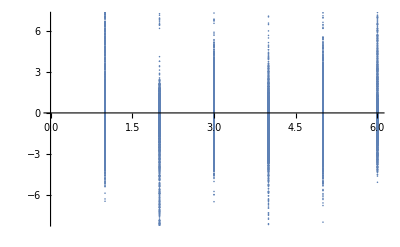
{17651.,{{{Symmetric case,{kn_similarity→{1.17504,8.78877},_sq (kn_similarity)→{-5.15501,0.351712},cites_size→{-1.11253,1.24537},cites_experience→1,cites_rankcmd→{0.158782,2.63784},domain_similarity→{1.29521,4.22655}}},{1}},-Graphics-}}
 |  |  |  |

```mathematica
(Print["Starting pointIdentified process where alpha = ",alpha];
pointIdentified=pointIdentifiedCR[ssSize,numSubsamples,sol[[2]], Cx[noAttr-1], groupIDs, dataArray,method,True,confidenceLevel->(1-alpha),asymptotics->nests, progressUpdate->10,useSavedGroups->True];
{{pointIdentified[[1,1]],pointIdentified[[2]]},
ListPlot@Flatten[Map[
MapIndexed[Flatten@{#2,#1}&,#]&,
pointIdentified[[-1]]
],1]
})//AbsoluteTiming
```